# Solvated Conformers for DrugBank’s Approved Drug Library

## By Madeleine Sutherland

## Introduction

### Purpose

The purpose of this project was to take the organic molecules from Drug Bank’s library of approved drugs, generate diverse conformers for each molecule, and optimize those conformers’ geometries to better reflect the pose(s) the given molecule would adopt in water.

#### Example: Erythromycin

Let’s show what we did with one example molecule, the antibiotic erythromycin.

```mathematica
erySMILES="CC[C@H]([C@](C)([C@@H]([C@@H](C)C([C@H](C)C[C@](C)([C@@H]([C@@H](C)[C@@H]([C@H]1C)O[C@@H](C[C@@]2(C)OC)O[C@@H](C)[C@@H]2O)O[C@@H]([C@@H]2O)O[C@H](C)C[C@@H]2N(C)C)O)=O)O)O)OC1=O"
```

CC[C@H]([C@](C)([C@@H]([C@@H](C)C([C@H](C)C[C@](C)([C@@H]([C@@H](C)[C@@H]([C@H]1C)O[C@@H](C[C@@]2(C)OC)O[C@@H](C)[C@@H]2O)O[C@@H]([C@@H]2O)O[C@H](C)C[C@@H]2N(C)C)O)=O)O)O)OC1=O

```mathematica
eryStartGeo=Molecule[erySMILES]
```

Molecule[…]

The next two lines of code define the molecular geometries for this demonstration:

```mathematica
{startconf1,startconf2,startconf3,optconf1,optconf2,optconf3}=
{Molecule[…],Molecule[…],Molecule[…],Molecule[…],Molecule[…],Molecule[…]}
```

{Molecule[…],Molecule[…],Molecule[…],Molecule[…],Molecule[…],Molecule[…]}

```mathematica
{startconf2Aligned,startconf3Aligned,optconf2Aligned,optconf3Aligned}={MoleculeAlign[startconf1,startconf2],MoleculeAlign[startconf1,startconf3],MoleculeAlign[optconf1,optconf2],MoleculeAlign[optconf1,optconf3]}
```

{Molecule[…],Molecule[…],Molecule[…],Molecule[…]}

```mathematica
AnnotatedArrow2[p_,q_,label_]:={Arrowheads[{{0},{.1,.5,Graphics[Inset[Style[label,Medium],{Left,Top}]]},{.1,1}}],Arrow[{p,q}]}(*Modified from a function in the documentation for Arrow*)
```

Here’s the whole trajectory from SMILES string to finished project:

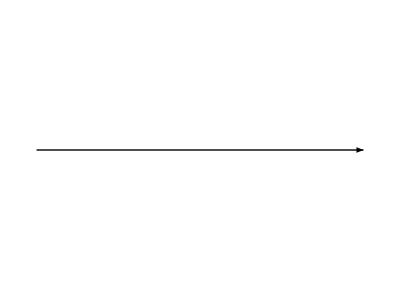
Erythromycin SMILES | -Graphics- | -Graphics3D- | -Graphics- | -Graphics3D- | -Graphics- | -Graphics3D-

```mathematica
Grid[{{
"Erythromycin SMILES",
Graphics[{Arrowheads[.2],AnnotatedArrow2[{0,0},{1,0},"Molecule[]"]}],
MoleculePlot3D[eryStartGeo],
Graphics[{Arrowheads[.2],AnnotatedArrow2[{0,0},{1,0},"Conformer Driving"]}],
Show[MoleculePlot3D[startconf1,ColorRules->{"C"->Darker[Cyan]}],MoleculePlot3D[startconf2Aligned,ColorRules->{"C"->Yellow}],
MoleculePlot3D[startconf3Aligned,ColorRules->{"C"->Purple}]],
Graphics[{Arrowheads[.2],AnnotatedArrow2[{0,0},{1,0},"Geom. Optimization"]}],
Show[MoleculePlot3D[optconf1,ColorRules->{"C"->Darker[Cyan]}],MoleculePlot3D[optconf2Aligned,ColorRules->{"C"->Yellow}],
MoleculePlot3D[optconf3Aligned,ColorRules->{"C"->Purple}]]
}}]
```

Above, the gray molecule is just the 3D geometry of erythromycin as built by Mathematica’s SMILES interpreter. The first set of colorful molecules are the product of molecular mechanics based conformer driving in Open Babel1 followed by a filtering step run in Python. The second set of colorful molecules are the conformers’ geometries after optimization in MOPAC2 using the PM7 Hamiltonian and the COSMO solvent model. One beautiful observation is that the three conformers’ geometries appear to have diverged a bit from each other at the end.

### Methodology Overview

A list of approved drug molecules’ names and SMILES identifiers was generated from the Drug Bank database3. My collaborator at ETH Zürich, Janina Kaderli, ran a round of desalting and duplicate removal and gave me a filtered library of molecules. I used a python script to extract a list of the SMILES identifier strings, and imported them into Mathematica. 

Starting with the list of SMILES strings, a lot of manipulations were needed. Here’s the breakdown of where I did each of the manipulations:

```mathematica
Dataset[{{"Remove molecules I don't want to optimize based on defined criteria","Mathematica"},{"Generate 3D starting geometries","Mostly Mathematica"},{"Run conformer driving","Open Babel"},
{"Initial filtering of conformers","Python"},
{"Conformer geometry optimization","MOPAC"},
{"Diagnose failed jobs","Mathematica"},
{"Visualize conformers' evolution","Mathematica"}}]
```

## Mathematica Steps in More Detail

### Removing molecules I don’t want to optimize

Here’s a subset of 50 molecules I can demonstrate with:

```mathematica
smiles2Dem={"CC[C@H](C)[C@@H](C(N(CCC1)[C@@H]1C(N[C@@H](CCC(O)=O)C(N[C@@H](CCC(O)=O)C(N[C@@H](Cc(cc1)ccc1O)C(N[C@@H](CC(C)C)C(O)=O)=O)=O)=O)=O)=O)NC([C@H](CCC(O)=O)NC([C@H](CCC(O)=O)NC([C@H](Cc1ccccc1)NC([C@H](CC(O)=O)NC(CNC([C@H](CC(N)=O)NC(CNC(CNC(CNC(CNC([C@H](CCC1)N1C([C@H](CCCNC(N)=N)NC([C@H](CCC1)N1C([C@@H](Cc1ccccc1)N)=O)=O)=O)=O)=O)=O)=O)=O)=O)=O)=O)=O)=O)=O","CCNC([C@H](CCC1)N1C([C@H](CCCNC(N)=N)NC([C@H](CC(C)C)NC([C@@H](CC(C)C)NC([C@H](Cc(cc1)ccc1O)NC([C@H](CO)NC([C@H](Cc1c[nH]c2c1cccc2)NC([C@H](Cc1c[nH]cn1)NC([C@H](CC1)NC1=O)=O)=O)=O)=O)=O)=O)=O)=O)=O","CC(C)C[C@@H](C(N[C@@H](CCCN=C(N)N)C(N(CCC1)[C@@H]1C(NNC(N)=O)=O)=O)=O)NC([C@@H](COC(C)(C)C)NC([C@H](Cc(cc1)ccc1O)NC([C@H](CO)NC([C@H](Cc1c[nH]c2c1cccc2)NC([C@H](Cc1cnc[nH]1)NC([C@H](CC1)NC1=O)=O)=O)=O)=O)=O)=O","CC(C)C[C@H](C(N[C@@H](C)C(N[C@H](C(C)C)C(N[C@@H](C(C)C)C(N[C@H](C(C)C)C(N[C@@H](Cc1c[nH]c2c1cccc2)C(N[C@H](CC(C)C)C(N[C@@H](Cc1c[nH]c2c1cccc2)C(N[C@H](CC(C)C)C(N[C@@H](Cc1c[nH]c2c1cccc2)C(N[C@H](CC(C)C)C(N[C@@H](Cc1c[nH]c2c1cccc2)C(NCCO)=O)=O)=O)=O)=O)=O)=O)=O)=O)=O)=O)=O)NC(CNC([C@H](C(C)C)NC=O)=O)=O","NC(CC[C@@H](C(N[C@@H](CC(N)=O)C(N[C@@H](CSSCCC(N[C@@H](Cc(cc1)ccc1O)C(N[C@H]1Cc2ccccc2)=O)=O)C(N(CCC2)[C@@H]2C(N[C@H](CCCNC(N)=N)C(NCC(N)=O)=O)=O)=O)=O)=O)NC1=O)=O","CC(C)C[C@@H](C(N[C@@H](CCCNC(N)=N)C(N(CCC1)[C@@H]1C(N[C@H](C)C(N)=O)=O)=O)=O)NC([C@@H](CCCNC(N)=O)NC([C@H](Cc(cc1)ccc1O)NC([C@H](CO)NC([C@@H](Cc1cnccc1)NC([C@@H](Cc(cc1)ccc1Cl)NC([C@@H](Cc1cc2ccccc2cc1)NC(C)=O)=O)=O)=O)=O)=O)=O","NC(CSSCC(C(N(CCC1)C1C(NC(CCCN=C(N)N)C(NCC(N)=O)=O)=O)=O)NC(C(CC(N)=O)NC(C(CCC(N)=O)NC(C(Cc1ccccc1)NC(C(Cc(cc1)ccc1O)N1)=O)=O)=O)=O)C1=O","NCCCCC(C(NCC(N)=O)=O)NC(C(CCC1)N1C(C(CSSCC(C(NC(Cc(cc1)ccc1O)C(NC(Cc1ccccc1)C(NC(CCC(N)=O)C(NC1CC(N)=O)=O)=O)=O)=O)N)NC1=O)=O)=O","CCCCCCCCCC(N[C@@H](Cc1c[nH]c2c1cccc2)C(N[C@H](CC(N)=O)C(N[C@@H](CC(O)=O)C(N[C@@H]([C@@H](C)OC([C@H](CC(c(cccc1)c1N)=O)NC([C@H]([C@H](C)CC(O)=O)NC([C@@H](CO)NC(CNC([C@H](CC(O)=O)NC([C@@H](C)NC([C@H](CC(O)=O)NC([C@H](CCCN)NC(CN1)=O)=O)=O)=O)=O)=O)=O)=O)=O)C1=O)=O)=O)=O)=O","CC[C@@H](C(N(C)CC(N(C)[C@@H](CC(C)C)C(N[C@@H](C(C)C)C(N(C)[C@@H](CC(C)C)C(N[C@@H](C)C(N[C@H](C)C(N(C)[C@@H](CC(C)C)C(N(C)[C@@H](CC(C)C)C(N(C)[C@@H](C(C)C)C(N(C)[C@H]1[C@@H]([C@H](C)C/C=C/C)O)=O)=O)=O)=O)=O)=O)=O)=O)=O)=O)NC1=O","C[C@H]([C@@H](CO)NC([C@H](CSSC[C@@H](C(N[C@@H](Cc1ccccc1)C(N[C@H](Cc1c[nH]c2c1cccc2)C(N[C@@H](CCCCN)C(N[C@H]1[C@@H](C)O)=O)=O)=O)=O)NC([C@@H](Cc2ccccc2)N)=O)NC1=O)=O)O","CC(C)C[C@@H](C(N[C@@H](CCCCNC(C)C)C(N(CCC1)[C@@H]1C(N[C@H](C)C(N)=O)=O)=O)=O)NC([C@@H](CC(N)=O)NC([C@H](Cc(cc1)ccc1O)N(C)C([C@H](CO)NC([C@@H](Cc1cnccc1)NC([C@@H](Cc(cc1)ccc1Cl)NC([C@@H](Cc1cc2ccccc2cc1)NC(C)=O)=O)=O)=O)=O)=O)=O","C[C@H](CNC(CC[C@](C)([C@H]1CC(N)=O)C(/C(/C)=C(/[C@@H](CCC(N)=O)C2(C)C)\\N=C2/C=C(/[C@@H](CCC(N)=O)[C@]2(C)CC(N)=O)\\N=C2/C(/C)=C2/[C@@H](CCC(N)=O)[C@]3(C)CC(N)=O)=N[C@H]1[C@]3(C)N2[Co+]C#N)=O)OP([O-])(O[C@H]([C@@H](CO)O[C@@H]1n2c(cc(C)c(C)c3)c3nc2)[C@H]1O)=O","CC(C)(C)OC(NCCC(N[C@@H](Cc1c[nH]c2c1cccc2)C(N[C@@H](CCSC)C(N[C@@H](CC(O)=O)C(N[C@@H](Cc1ccccc1)C(N)=O)=O)=O)=O)=O)=O","CC(C)C[C@@H](B(O)O)NC([C@H](Cc1ccccc1)NC(c1nccnc1)=O)=O","CC[C@H]([C@](C)([C@@H]([C@@H](C)C([C@H](C)C[C@](C)([C@@H]([C@@H](C)[C@@H]([C@H]1C)O[C@@H](C[C@@]2(C)OC)O[C@@H](C)[C@@H]2O)O[C@@H]([C@@H]2O)O[C@H](C)C[C@@H]2N(C)C)O)=O)O)O)OC1=O","C[C@H](CNC(CC[C@](C)([C@@H](CC(N)=O)[C@H]([C@@](C)([C@@](C)(CC(N)=O)[C@@H]1CCC(N)=O)[N+]2=C1C(C)=C([C@@](C)(CC(N)=O)[C@@H]1CCC(N)=O)[N+]3=C1C=C1C(C)(C)[C@@H]4CCC(N)=O)N56)C6=C(C)C4=[N+]1[Co-3]235([n+]1cn([C@H]([C@@H]2O)O[C@H](CO)[C@H]2O2)c3c1cc(C)c(C)c3)O)=O)OP2([O-])=O","CC[C@@H]([C@@](C)([C@H]([C@H](C)N(C)C[C@@H](C)C[C@@](C)([C@H]([C@H](C)[C@H]([C@@H]1C)O[C@H](C[C@]2(C)OC)O[C@H](C)[C@H]2O)O[C@H]([C@H]2O)O[C@@H](C)C[C@H]2N(C)C)O)O)O)OC1=O","OC(C(O[C@@H]1C[C@H](CC2)[N+]3(CCCC3)[C@H]2C1)=O)(c1ccccc1)c1ccccc1","CCC1=C(C)CN(C(NCCc(cc2)ccc2S(NC(N[C@H]2CC[C@H](C)CC2)=O)(=O)=O)=O)C1=O","CNC(CN1(CCN2(CCN3(C4)CC([O-]5)=O)CC([O-]6)=O)CC([O-]7)=O)=O[Gd+3]123567O=C4NC","CN([C@H](CC1)C2)[C@@H]1C[C@H]2OC(c1ccccc1)c1ccccc1","C[C@@H]([C@H]([C@H]([C@H]([C@H](C(O)=C(C(N)=O)C1=O)N(C)C)[C@@]11O)O)C2=C1O)c1cccc(O)c1C2=O","C[C@@]([C@H](C[C@H]([C@H](C(O)=C(C(NCNCCCC[C@H](C(O)=O)N)=O)C1=O)N(C)C)[C@@]11O)C2=C1O)(c1cccc(O)c1C2=O)O","C[C@H]([C@H]([C@H](C)NC([C@@H]([C@@H](c1c[nH]cn1)OC(C(C1O)OC(C(C2OC(N)=O)O)OC(CO)C2O)OC(CO)C1O)NC(c1nc([C@@H](CC(N)=O)NC[C@H](C(N)=O)N)nc(N)c1C)=O)=O)O)C(N[C@H]([C@H](C)O)C(NCCc1nc(-c2nc(C(NCCC[S+](C)C)=O)cs2)cs1)=O)=O","CC(C)OC(OCOP(CO[C@H](C)Cn1c2ncnc(N)c2nc1)(OCOC(OC(C)C)=O)=O)=O","NC[C@H](CC1)CC[C@@H]1C(O)=O","CC[C@@](C[C@@H](C1)C[C@@]2(C(OC)=O)c(cc([C@@](CC3)([C@@H]4N3CC=C[C@]4(CC)[C@@H]([C@]3(C(N)=O)O)O)[C@@H]3N3C)c3c3)c3OC)(CN1CCc1c2[nH]c2c1cccc2)O","NCCC[C@@H](CC(NC[C@@H](C(N/C(/C(N[C@@H]([C@@H]1NC(N)=NCC1)C(NC[C@@H](C(N[C@H]1CO)=O)N)=O)=O)=C/NC(N)=O)=O)NC1=O)=O)N","C[C@@H](C(N[C@@H](CNC(C[C@H](CCCN)N)=O)C(N/C(/C(N[C@@H]([C@@H]1NC(N)=NCC1)C(NC[C@@H]1N)=O)=O)=C/NC(N)=O)=O)=O)NC1=O","N#C[Fe-2](C#N)(C#N)(C#N)(C#N)N=O","[O-]C(C([C@H]([C@@H]([C@H]([C@H](CO)O)O)O)O)O)=O","CC(C)[N+](C)([C@H](CC1)C2)[C@@H]1C[C@H]2OC(C(CO)c1ccccc1)=O","Cc1cc(C(N2CCN(C)CC2)=Nc(cccc2)c2N2)c2s1","CC[C@@H](/C=C(\\C)/C[C@@H](C)C[C@H]([C@@H]([C@@H](C[C@@H]1C)OC)O[C@@]1(C(C(N(CCCC1)[C@H]1C(O[C@H]([C@@H](C)[C@@H](C1)O)/C(/C)=C/[C@@H](CC[C@H]2Cl)C[C@@H]2OC)=O)=O)=O)O)OC)C1=O","Nc1cc(N2CCCCC2)nc(N)[n+]1[O-]","CC[C@]1([C@@H]([C@]([C@H]2N(C)c3c4)(C(OC)=O)O)OC(C)=O)C=CCN(CC5)[C@H]1[C@]25c3cc([C@@](C[C@H](C1)C=C(CC)CN1C1)(C(OC)=O)c2c1c(cccc1)c1[nH]2)c4OC","CCCCCOc(cc1)ccc1-c(cc1)ccc1-c(cc1)ccc1C(N[C@H](C[C@@H]([C@@H](NC([C@@H]([C@@H]([C@H](C)C1)O)N1C([C@@H]([C@H](C)O)NC([C@@H]([C@H]([C@@H](c(cc1)ccc1O)O)O)NC([C@@H](C[C@@H](C1)O)N1C([C@@H]([C@H](C)O)N1)=O)=O)=O)=O)=O)O)O)C1=O)=O","CN(CC1)CCN1C1=Nc(cc(cc2)Cl)c2Nc2c1cccc2","O[Al](O)OS(OC[C@@H]([C@@H]([C@H]1OS(O[Al](O)O)(=O)=O)OS(O[Al](O)O)(=O)=O)O[C@]1(COS(O[Al](O)O)(=O)=O)O[C@@H]([C@H]([C@@H]1OS(O[Al](O)O)(=O)=O)OS(O[Al](O)O)(=O)=O)O[C@@H](COS(O[Al](O)O)(=O)=O)[C@@H]1OS(O[Al](O)O)(=O)=O)(=O)=O","O[Al](O)O","CCCCC(OCC([C@](C[C@H](c1c(c(C(c(c2ccc3)c3OC)=O)c3C2=O)O)O[C@H](C[C@H]2NC(C(F)(F)F)=O)O[C@H](C)[C@@H]2O)(Cc1c3O)O)=O)=O","C[C@H]([C@H]([C@H](C1)O)O)O[C@H]1O[C@H]([C@@H](C)O[C@H](C1)O[C@H]([C@@H](C)O[C@H](C2)O[C@@H](CC3)C[C@@H](CC4)[C@@]3(C)[C@@H](C[C@H]([C@]3(C)[C@H](CC5)C(CO6)=CC6=O)O)[C@@H]4[C@]35O)[C@H]2O)[C@H]1O","C[C@H]([C@@H](C(NCC(N[C@@H](Cc1c[nH]c2c1cccc2)C(N[C@@H](CCSC)C(N[C@@H](CC(O)=O)C(N[C@@H](Cc1ccccc1)C(N)=O)=O)=O)=O)=O)=O)NC([C@H](Cc(cc1)ccc1OS(O)(=O)=O)NC([C@H](CC(O)=O)NC([C@H](CCC(N)=O)NC([C@H](CC1)NC1=O)=O)=O)=O)=O)O","C[C@@H]([C@H](C)O)[C@@H]1O[C@H]1C[C@@H](CO[C@@H](C/C(/C)=C/C(OCCCCCCCCC(O)=O)=O)[C@@H]1O)[C@H]1O","CN([C@H](CC1)C2)[C@@H]1C[C@H]2OC([C@H](CO)c1ccccc1)=O","CCCCC[C@@](C)(/C=C/[C@H]([C@@H](C/C=C\\CCCC(O)=O)[C@H](C1)O)[C@H]1O)O","Cl[C@H]([C@H]([C@@H]([C@@H]([C@H]1Cl)Cl)Cl)Cl)[C@H]1Cl","N=O","C[C@@]([C@@H]1C(OC)=O)(C(C(/C=C(/C(C)=C2C=C)\\N/C2=C\\C(C(C)=C2CCC(O)=O)=N/C2=C2)=N3)=CC=C1C(OC)=O)/C3=C/c1c(C)c(CCC(OC)=O)c2[nH]1"}
```

{CC[C@H](C)[C@@H](C(N(CCC1)[C@@H]1C(N[C@@H](CCC(O)=O)C(N[C@@H](CCC(O)=O)C(N[C@@H](Cc(cc1)ccc1O)C(N[C@@H](CC(C)C)C(O)=O)=O)=O)=O)=O)=O)NC([C@H](CCC(O)=O)NC([C@H](CCC(O)=O)NC([C@H](Cc1ccccc1)NC([C@H](CC(O)=O)NC(CNC([C@H](CC(N)=O)NC(CNC(CNC(CNC(CNC([C@H](CCC1)N1C([C@H](CCCNC(N)=N)NC([C@H](CCC1)N1C([C@@H](Cc1ccccc1)N)=O)=O)=O)=O)=O)=O)=O)=O)=O)=O)=O)=O)=O)=O,CCNC([C@H](CCC1)N1C([C@H](CCCNC(N)=N)NC([C@H](CC(C)C)NC([C@@H](CC(C)C)NC([C@H](Cc(cc1)ccc1O)NC([C@H](CO)NC([C@H](Cc1c[nH]c2c1cccc2)NC([C@H](Cc1c[nH]cn1)NC([C@H](CC1)NC1=O)=O)=O)=O)=O)=O)=O)=O)=O)=O,CC(C)C[C@@H](C(N[C@@H](CCCN=C(N)N)C(N(CCC1)[C@@H]1C(NNC(N)=O)=O)=O)=O)NC([C@@H](COC(C)(C)C)NC([C@H](Cc(cc1)ccc1O)NC([C@H](CO)NC([C@H](Cc1c[nH]c2c1cccc2)NC([C@H](Cc1cnc[nH]1)NC([C@H](CC1)NC1=O)=O)=O)=O)=O)=O)=O,CC(C)C[C@H](C(N[C@@H](C)C(N[C@H](C(C)C)C(N[C@@H](C(C)C)C(N[C@H](C(C)C)C(N[C@@H](Cc1c[nH]c2c1cccc2)C(N[C@H](CC(C)C)C(N[C@@H](Cc1c[nH]c2c1cccc2)C(N[C@H](CC(C)C)C(N[C@@H](Cc1c[nH]c2c1cccc2)C(N[C@H](CC(C)C)C(N[C@@H](Cc1c[nH]c2c1cccc2)C(NCCO)=O)=O)=O)=O)=O)=O)=O)=O)=O)=O)=O)=O)NC(CNC([C@H](C(C)C)NC=O)=O)=O,NC(CC[C@@H](C(N[C@@H](CC(N)=O)C(N[C@@H](CSSCCC(N[C@@H](Cc(cc1)ccc1O)C(N[C@H]1Cc2ccccc2)=O)=O)C(N(CCC2)[C@@H]2C(N[C@H](CCCNC(N)=N)C(NCC(N)=O)=O)=O)=O)=O)=O)NC1=O)=O,CC(C)C[C@@H](C(N[C@@H](CCCNC(N)=N)C(N(CCC1)[C@@H]1C(N[C@H](C)C(N)=O)=O)=O)=O)NC([C@@H](CCCNC(N)=O)NC([C@H](Cc(cc1)ccc1O)NC([C@H](CO)NC([C@@H](Cc1cnccc1)NC([C@@H](Cc(cc1)ccc1Cl)NC([C@@H](Cc1cc2ccccc2cc1)NC(C)=O)=O)=O)=O)=O)=O)=O,NC(CSSCC(C(N(CCC1)C1C(NC(CCCN=C(N)N)C(NCC(N)=O)=O)=O)=O)NC(C(CC(N)=O)NC(C(CCC(N)=O)NC(C(Cc1ccccc1)NC(C(Cc(cc1)ccc1O)N1)=O)=O)=O)=O)C1=O,NCCCCC(C(NCC(N)=O)=O)NC(C(CCC1)N1C(C(CSSCC(C(NC(Cc(cc1)ccc1O)C(NC(Cc1ccccc1)C(NC(CCC(N)=O)C(NC1CC(N)=O)=O)=O)=O)=O)N)NC1=O)=O)=O,CCCCCCCCCC(N[C@@H](Cc1c[nH]c2c1cccc2)C(N[C@H](CC(N)=O)C(N[C@@H](CC(O)=O)C(N[C@@H]([C@@H](C)OC([C@H](CC(c(cccc1)c1N)=O)NC([C@H]([C@H](C)CC(O)=O)NC([C@@H](CO)NC(CNC([C@H](CC(O)=O)NC([C@@H](C)NC([C@H](CC(O)=O)NC([C@H](CCCN)NC(CN1)=O)=O)=O)=O)=O)=O)=O)=O)=O)C1=O)=O)=O)=O)=O,CC[C@@H](C(N(C)CC(N(C)[C@@H](CC(C)C)C(N[C@@H](C(C)C)C(N(C)[C@@H](CC(C)C)C(N[C@@H](C)C(N[C@H](C)C(N(C)[C@@H](CC(C)C)C(N(C)[C@@H](CC(C)C)C(N(C)[C@@H](C(C)C)C(N(C)[C@H]1[C@@H]([C@H](C)C/C=C/C)O)=O)=O)=O)=O)=O)=O)=O)=O)=O)=O)NC1=O,C[C@H]([C@@H](CO)NC([C@H](CSSC[C@@H](C(N[C@@H](Cc1ccccc1)C(N[C@H](Cc1c[nH]c2c1cccc2)C(N[C@@H](CCCCN)C(N[C@H]1[C@@H](C)O)=O)=O)=O)=O)NC([C@@H](Cc2ccccc2)N)=O)NC1=O)=O)O,CC(C)C[C@@H](C(N[C@@H](CCCCNC(C)C)C(N(CCC1)[C@@H]1C(N[C@H](C)C(N)=O)=O)=O)=O)NC([C@@H](CC(N)=O)NC([C@H](Cc(cc1)ccc1O)N(C)C([C@H](CO)NC([C@@H](Cc1cnccc1)NC([C@@H](Cc(cc1)ccc1Cl)NC([C@@H](Cc1cc2ccccc2cc1)NC(C)=O)=O)=O)=O)=O)=O)=O,C[C@H](CNC(CC[C@](C)([C@H]1CC(N)=O)C(/C(/C)=C(/[C@@H](CCC(N)=O)C2(C)C)\N=C2/C=C(/[C@@H](CCC(N)=O)[C@]2(C)CC(N)=O)\N=C2/C(/C)=C2/[C@@H](CCC(N)=O)[C@]3(C)CC(N)=O)=N[C@H]1[C@]3(C)N2[Co+]C#N)=O)OP([O-])(O[C@H]([C@@H](CO)O[C@@H]1n2c(cc(C)c(C)c3)c3nc2)[C@H]1O)=O,CC(C)(C)OC(NCCC(N[C@@H](Cc1c[nH]c2c1cccc2)C(N[C@@H](CCSC)C(N[C@@H](CC(O)=O)C(N[C@@H](Cc1ccccc1)C(N)=O)=O)=O)=O)=O)=O,CC(C)C[C@@H](B(O)O)NC([C@H](Cc1ccccc1)NC(c1nccnc1)=O)=O,CC[C@H]([C@](C)([C@@H]([C@@H](C)C([C@H](C)C[C@](C)([C@@H]([C@@H](C)[C@@H]([C@H]1C)O[C@@H](C[C@@]2(C)OC)O[C@@H](C)[C@@H]2O)O[C@@H]([C@@H]2O)O[C@H](C)C[C@@H]2N(C)C)O)=O)O)O)OC1=O,C[C@H](CNC(CC[C@](C)([C@@H](CC(N)=O)[C@H]([C@@](C)([C@@](C)(CC(N)=O)[C@@H]1CCC(N)=O)[N+]2=C1C(C)=C([C@@](C)(CC(N)=O)[C@@H]1CCC(N)=O)[N+]3=C1C=C1C(C)(C)[C@@H]4CCC(N)=O)N56)C6=C(C)C4=[N+]1[Co-3]235([n+]1cn([C@H]([C@@H]2O)O[C@H](CO)[C@H]2O2)c3c1cc(C)c(C)c3)O)=O)OP2([O-])=O,CC[C@@H]([C@@](C)([C@H]([C@H](C)N(C)C[C@@H](C)C[C@@](C)([C@H]([C@H](C)[C@H]([C@@H]1C)O[C@H](C[C@]2(C)OC)O[C@H](C)[C@H]2O)O[C@H]([C@H]2O)O[C@@H](C)C[C@H]2N(C)C)O)O)O)OC1=O,OC(C(O[C@@H]1C[C@H](CC2)[N+]3(CCCC3)[C@H]2C1)=O)(c1ccccc1)c1ccccc1,CCC1=C(C)CN(C(NCCc(cc2)ccc2S(NC(N[C@H]2CC[C@H](C)CC2)=O)(=O)=O)=O)C1=O,CNC(CN1(CCN2(CCN3(C4)CC([O-]5)=O)CC([O-]6)=O)CC([O-]7)=O)=O[Gd+3]123567O=C4NC,CN([C@H](CC1)C2)[C@@H]1C[C@H]2OC(c1ccccc1)c1ccccc1,C[C@@H]([C@H]([C@H]([C@H]([C@H](C(O)=C(C(N)=O)C1=O)N(C)C)[C@@]11O)O)C2=C1O)c1cccc(O)c1C2=O,C[C@@]([C@H](C[C@H]([C@H](C(O)=C(C(NCNCCCC[C@H](C(O)=O)N)=O)C1=O)N(C)C)[C@@]11O)C2=C1O)(c1cccc(O)c1C2=O)O,C[C@H]([C@H]([C@H](C)NC([C@@H]([C@@H](c1c[nH]cn1)OC(C(C1O)OC(C(C2OC(N)=O)O)OC(CO)C2O)OC(CO)C1O)NC(c1nc([C@@H](CC(N)=O)NC[C@H](C(N)=O)N)nc(N)c1C)=O)=O)O)C(N[C@H]([C@H](C)O)C(NCCc1nc(-c2nc(C(NCCC[S+](C)C)=O)cs2)cs1)=O)=O,CC(C)OC(OCOP(CO[C@H](C)Cn1c2ncnc(N)c2nc1)(OCOC(OC(C)C)=O)=O)=O,NC[C@H](CC1)CC[C@@H]1C(O)=O,CC[C@@](C[C@@H](C1)C[C@@]2(C(OC)=O)c(cc([C@@](CC3)([C@@H]4N3CC=C[C@]4(CC)[C@@H]([C@]3(C(N)=O)O)O)[C@@H]3N3C)c3c3)c3OC)(CN1CCc1c2[nH]c2c1cccc2)O,NCCC[C@@H](CC(NC[C@@H](C(N/C(/C(N[C@@H]([C@@H]1NC(N)=NCC1)C(NC[C@@H](C(N[C@H]1CO)=O)N)=O)=O)=C/NC(N)=O)=O)NC1=O)=O)N,C[C@@H](C(N[C@@H](CNC(C[C@H](CCCN)N)=O)C(N/C(/C(N[C@@H]([C@@H]1NC(N)=NCC1)C(NC[C@@H]1N)=O)=O)=C/NC(N)=O)=O)=O)NC1=O,N#C[Fe-2](C#N)(C#N)(C#N)(C#N)N=O,[O-]C(C([C@H]([C@@H]([C@H]([C@H](CO)O)O)O)O)O)=O,CC(C)[N+](C)([C@H](CC1)C2)[C@@H]1C[C@H]2OC(C(CO)c1ccccc1)=O,Cc1cc(C(N2CCN(C)CC2)=Nc(cccc2)c2N2)c2s1,CC[C@@H](/C=C(\C)/C[C@@H](C)C[C@H]([C@@H]([C@@H](C[C@@H]1C)OC)O[C@@]1(C(C(N(CCCC1)[C@H]1C(O[C@H]([C@@H](C)[C@@H](C1)O)/C(/C)=C/[C@@H](CC[C@H]2Cl)C[C@@H]2OC)=O)=O)=O)O)OC)C1=O,Nc1cc(N2CCCCC2)nc(N)[n+]1[O-],CC[C@]1([C@@H]([C@]([C@H]2N(C)c3c4)(C(OC)=O)O)OC(C)=O)C=CCN(CC5)[C@H]1[C@]25c3cc([C@@](C[C@H](C1)C=C(CC)CN1C1)(C(OC)=O)c2c1c(cccc1)c1[nH]2)c4OC,CCCCCOc(cc1)ccc1-c(cc1)ccc1-c(cc1)ccc1C(N[C@H](C[C@@H]([C@@H](NC([C@@H]([C@@H]([C@H](C)C1)O)N1C([C@@H]([C@H](C)O)NC([C@@H]([C@H]([C@@H](c(cc1)ccc1O)O)O)NC([C@@H](C[C@@H](C1)O)N1C([C@@H]([C@H](C)O)N1)=O)=O)=O)=O)=O)O)O)C1=O)=O,CN(CC1)CCN1C1=Nc(cc(cc2)Cl)c2Nc2c1cccc2,O[Al](O)OS(OC[C@@H]([C@@H]([C@H]1OS(O[Al](O)O)(=O)=O)OS(O[Al](O)O)(=O)=O)O[C@]1(COS(O[Al](O)O)(=O)=O)O[C@@H]([C@H]([C@@H]1OS(O[Al](O)O)(=O)=O)OS(O[Al](O)O)(=O)=O)O[C@@H](COS(O[Al](O)O)(=O)=O)[C@@H]1OS(O[Al](O)O)(=O)=O)(=O)=O,O[Al](O)O,CCCCC(OCC([C@](C[C@H](c1c(c(C(c(c2ccc3)c3OC)=O)c3C2=O)O)O[C@H](C[C@H]2NC(C(F)(F)F)=O)O[C@H](C)[C@@H]2O)(Cc1c3O)O)=O)=O,C[C@H]([C@H]([C@H](C1)O)O)O[C@H]1O[C@H]([C@@H](C)O[C@H](C1)O[C@H]([C@@H](C)O[C@H](C2)O[C@@H](CC3)C[C@@H](CC4)[C@@]3(C)[C@@H](C[C@H]([C@]3(C)[C@H](CC5)C(CO6)=CC6=O)O)[C@@H]4[C@]35O)[C@H]2O)[C@H]1O,C[C@H]([C@@H](C(NCC(N[C@@H](Cc1c[nH]c2c1cccc2)C(N[C@@H](CCSC)C(N[C@@H](CC(O)=O)C(N[C@@H](Cc1ccccc1)C(N)=O)=O)=O)=O)=O)=O)NC([C@H](Cc(cc1)ccc1OS(O)(=O)=O)NC([C@H](CC(O)=O)NC([C@H](CCC(N)=O)NC([C@H](CC1)NC1=O)=O)=O)=O)=O)O,C[C@@H]([C@H](C)O)[C@@H]1O[C@H]1C[C@@H](CO[C@@H](C/C(/C)=C/C(OCCCCCCCCC(O)=O)=O)[C@@H]1O)[C@H]1O,CN([C@H](CC1)C2)[C@@H]1C[C@H]2OC([C@H](CO)c1ccccc1)=O,CCCCC[C@@](C)(/C=C/[C@H]([C@@H](C/C=C\CCCC(O)=O)[C@H](C1)O)[C@H]1O)O,Cl[C@H]([C@H]([C@@H]([C@@H]([C@H]1Cl)Cl)Cl)Cl)[C@H]1Cl,N=O,C[C@@]([C@@H]1C(OC)=O)(C(C(/C=C(/C(C)=C2C=C)\N/C2=C\C(C(C)=C2CCC(O)=O)=N/C2=C2)=N3)=CC=C1C(OC)=O)/C3=C/c1c(C)c(CCC(OC)=O)c2[nH]1}

I need to extract lists of atomic numbers from these SMILES strings:

```mathematica
atomListExtractor[string_]:=AtomList[Molecule[string],Atom[_],"AtomicNumber"]
```

```mathematica
SetAttributes[atomListExtractor,Listable]
```

```mathematica
atomLists=atomListExtractor[smiles2Dem];
```

Molecule::valenc: Invalid valence for nitrogen atom at position 5.

The three classes of compounds I don’t wish to simulate right now are:

Fewer than 3 heavy atoms (because for such compounds, my conformer generation and refinement process is a phantasmagorical waste of time)

Inorganic

Containing a transition or post-transition metal.

The next function will sort away those compounds.

```mathematica
moleculesorter[list_]:=If[Length[DeleteCases[list,1]]<3||ContainsAny[list,tmLAPostTMNums]||ContainsNone[list,{6}],no,yes]
```

```mathematica
yesAndNoDem=Map[moleculesorter,atomLists,{-2}]
```

{yes,yes,yes,yes,yes,yes,yes,yes,yes,yes,yes,yes,no,yes,yes,yes,no,yes,yes,yes,no,yes,yes,yes,yes,yes,yes,yes,yes,yes,no,yes,yes,yes,yes,yes,yes,yes,yes,no,no,yes,yes,yes,yes,yes,yes,yes,no,yes}

Now I will put the compounds I actually want to work with into a new list:

```mathematica
yesIndices=Flatten@Position[yesAndNoDem,yes]
```

{1,2,3,4,5,6,7,8,9,10,11,12,14,15,16,18,19,20,22,23,24,25,26,27,28,29,30,32,33,34,35,36,37,38,39,42,43,44,45,46,47,48,50}

```mathematica
Length[yesIndices]
```

43

```mathematica
compoundsToSimulate=smiles2Dem[[yesIndices]]
```

{CC[C@H](C)[C@@H](C(N(CCC1)[C@@H]1C(N[C@@H](CCC(O)=O)C(N[C@@H](CCC(O)=O)C(N[C@@H](Cc(cc1)ccc1O)C(N[C@@H](CC(C)C)C(O)=O)=O)=O)=O)=O)=O)NC([C@H](CCC(O)=O)NC([C@H](CCC(O)=O)NC([C@H](Cc1ccccc1)NC([C@H](CC(O)=O)NC(CNC([C@H](CC(N)=O)NC(CNC(CNC(CNC(CNC([C@H](CCC1)N1C([C@H](CCCNC(N)=N)NC([C@H](CCC1)N1C([C@@H](Cc1ccccc1)N)=O)=O)=O)=O)=O)=O)=O)=O)=O)=O)=O)=O)=O)=O,CCNC([C@H](CCC1)N1C([C@H](CCCNC(N)=N)NC([C@H](CC(C)C)NC([C@@H](CC(C)C)NC([C@H](Cc(cc1)ccc1O)NC([C@H](CO)NC([C@H](Cc1c[nH]c2c1cccc2)NC([C@H](Cc1c[nH]cn1)NC([C@H](CC1)NC1=O)=O)=O)=O)=O)=O)=O)=O)=O)=O,CC(C)C[C@@H](C(N[C@@H](CCCN=C(N)N)C(N(CCC1)[C@@H]1C(NNC(N)=O)=O)=O)=O)NC([C@@H](COC(C)(C)C)NC([C@H](Cc(cc1)ccc1O)NC([C@H](CO)NC([C@H](Cc1c[nH]c2c1cccc2)NC([C@H](Cc1cnc[nH]1)NC([C@H](CC1)NC1=O)=O)=O)=O)=O)=O)=O,CC(C)C[C@H](C(N[C@@H](C)C(N[C@H](C(C)C)C(N[C@@H](C(C)C)C(N[C@H](C(C)C)C(N[C@@H](Cc1c[nH]c2c1cccc2)C(N[C@H](CC(C)C)C(N[C@@H](Cc1c[nH]c2c1cccc2)C(N[C@H](CC(C)C)C(N[C@@H](Cc1c[nH]c2c1cccc2)C(N[C@H](CC(C)C)C(N[C@@H](Cc1c[nH]c2c1cccc2)C(NCCO)=O)=O)=O)=O)=O)=O)=O)=O)=O)=O)=O)=O)NC(CNC([C@H](C(C)C)NC=O)=O)=O,NC(CC[C@@H](C(N[C@@H](CC(N)=O)C(N[C@@H](CSSCCC(N[C@@H](Cc(cc1)ccc1O)C(N[C@H]1Cc2ccccc2)=O)=O)C(N(CCC2)[C@@H]2C(N[C@H](CCCNC(N)=N)C(NCC(N)=O)=O)=O)=O)=O)=O)NC1=O)=O,CC(C)C[C@@H](C(N[C@@H](CCCNC(N)=N)C(N(CCC1)[C@@H]1C(N[C@H](C)C(N)=O)=O)=O)=O)NC([C@@H](CCCNC(N)=O)NC([C@H](Cc(cc1)ccc1O)NC([C@H](CO)NC([C@@H](Cc1cnccc1)NC([C@@H](Cc(cc1)ccc1Cl)NC([C@@H](Cc1cc2ccccc2cc1)NC(C)=O)=O)=O)=O)=O)=O)=O,NC(CSSCC(C(N(CCC1)C1C(NC(CCCN=C(N)N)C(NCC(N)=O)=O)=O)=O)NC(C(CC(N)=O)NC(C(CCC(N)=O)NC(C(Cc1ccccc1)NC(C(Cc(cc1)ccc1O)N1)=O)=O)=O)=O)C1=O,NCCCCC(C(NCC(N)=O)=O)NC(C(CCC1)N1C(C(CSSCC(C(NC(Cc(cc1)ccc1O)C(NC(Cc1ccccc1)C(NC(CCC(N)=O)C(NC1CC(N)=O)=O)=O)=O)=O)N)NC1=O)=O)=O,CCCCCCCCCC(N[C@@H](Cc1c[nH]c2c1cccc2)C(N[C@H](CC(N)=O)C(N[C@@H](CC(O)=O)C(N[C@@H]([C@@H](C)OC([C@H](CC(c(cccc1)c1N)=O)NC([C@H]([C@H](C)CC(O)=O)NC([C@@H](CO)NC(CNC([C@H](CC(O)=O)NC([C@@H](C)NC([C@H](CC(O)=O)NC([C@H](CCCN)NC(CN1)=O)=O)=O)=O)=O)=O)=O)=O)=O)C1=O)=O)=O)=O)=O,CC[C@@H](C(N(C)CC(N(C)[C@@H](CC(C)C)C(N[C@@H](C(C)C)C(N(C)[C@@H](CC(C)C)C(N[C@@H](C)C(N[C@H](C)C(N(C)[C@@H](CC(C)C)C(N(C)[C@@H](CC(C)C)C(N(C)[C@@H](C(C)C)C(N(C)[C@H]1[C@@H]([C@H](C)C/C=C/C)O)=O)=O)=O)=O)=O)=O)=O)=O)=O)=O)NC1=O,C[C@H]([C@@H](CO)NC([C@H](CSSC[C@@H](C(N[C@@H](Cc1ccccc1)C(N[C@H](Cc1c[nH]c2c1cccc2)C(N[C@@H](CCCCN)C(N[C@H]1[C@@H](C)O)=O)=O)=O)=O)NC([C@@H](Cc2ccccc2)N)=O)NC1=O)=O)O,CC(C)C[C@@H](C(N[C@@H](CCCCNC(C)C)C(N(CCC1)[C@@H]1C(N[C@H](C)C(N)=O)=O)=O)=O)NC([C@@H](CC(N)=O)NC([C@H](Cc(cc1)ccc1O)N(C)C([C@H](CO)NC([C@@H](Cc1cnccc1)NC([C@@H](Cc(cc1)ccc1Cl)NC([C@@H](Cc1cc2ccccc2cc1)NC(C)=O)=O)=O)=O)=O)=O)=O,CC(C)(C)OC(NCCC(N[C@@H](Cc1c[nH]c2c1cccc2)C(N[C@@H](CCSC)C(N[C@@H](CC(O)=O)C(N[C@@H](Cc1ccccc1)C(N)=O)=O)=O)=O)=O)=O,CC(C)C[C@@H](B(O)O)NC([C@H](Cc1ccccc1)NC(c1nccnc1)=O)=O,CC[C@H]([C@](C)([C@@H]([C@@H](C)C([C@H](C)C[C@](C)([C@@H]([C@@H](C)[C@@H]([C@H]1C)O[C@@H](C[C@@]2(C)OC)O[C@@H](C)[C@@H]2O)O[C@@H]([C@@H]2O)O[C@H](C)C[C@@H]2N(C)C)O)=O)O)O)OC1=O,CC[C@@H]([C@@](C)([C@H]([C@H](C)N(C)C[C@@H](C)C[C@@](C)([C@H]([C@H](C)[C@H]([C@@H]1C)O[C@H](C[C@]2(C)OC)O[C@H](C)[C@H]2O)O[C@H]([C@H]2O)O[C@@H](C)C[C@H]2N(C)C)O)O)O)OC1=O,OC(C(O[C@@H]1C[C@H](CC2)[N+]3(CCCC3)[C@H]2C1)=O)(c1ccccc1)c1ccccc1,CCC1=C(C)CN(C(NCCc(cc2)ccc2S(NC(N[C@H]2CC[C@H](C)CC2)=O)(=O)=O)=O)C1=O,CN([C@H](CC1)C2)[C@@H]1C[C@H]2OC(c1ccccc1)c1ccccc1,C[C@@H]([C@H]([C@H]([C@H]([C@H](C(O)=C(C(N)=O)C1=O)N(C)C)[C@@]11O)O)C2=C1O)c1cccc(O)c1C2=O,C[C@@]([C@H](C[C@H]([C@H](C(O)=C(C(NCNCCCC[C@H](C(O)=O)N)=O)C1=O)N(C)C)[C@@]11O)C2=C1O)(c1cccc(O)c1C2=O)O,C[C@H]([C@H]([C@H](C)NC([C@@H]([C@@H](c1c[nH]cn1)OC(C(C1O)OC(C(C2OC(N)=O)O)OC(CO)C2O)OC(CO)C1O)NC(c1nc([C@@H](CC(N)=O)NC[C@H](C(N)=O)N)nc(N)c1C)=O)=O)O)C(N[C@H]([C@H](C)O)C(NCCc1nc(-c2nc(C(NCCC[S+](C)C)=O)cs2)cs1)=O)=O,CC(C)OC(OCOP(CO[C@H](C)Cn1c2ncnc(N)c2nc1)(OCOC(OC(C)C)=O)=O)=O,NC[C@H](CC1)CC[C@@H]1C(O)=O,CC[C@@](C[C@@H](C1)C[C@@]2(C(OC)=O)c(cc([C@@](CC3)([C@@H]4N3CC=C[C@]4(CC)[C@@H]([C@]3(C(N)=O)O)O)[C@@H]3N3C)c3c3)c3OC)(CN1CCc1c2[nH]c2c1cccc2)O,NCCC[C@@H](CC(NC[C@@H](C(N/C(/C(N[C@@H]([C@@H]1NC(N)=NCC1)C(NC[C@@H](C(N[C@H]1CO)=O)N)=O)=O)=C/NC(N)=O)=O)NC1=O)=O)N,C[C@@H](C(N[C@@H](CNC(C[C@H](CCCN)N)=O)C(N/C(/C(N[C@@H]([C@@H]1NC(N)=NCC1)C(NC[C@@H]1N)=O)=O)=C/NC(N)=O)=O)=O)NC1=O,[O-]C(C([C@H]([C@@H]([C@H]([C@H](CO)O)O)O)O)O)=O,CC(C)[N+](C)([C@H](CC1)C2)[C@@H]1C[C@H]2OC(C(CO)c1ccccc1)=O,Cc1cc(C(N2CCN(C)CC2)=Nc(cccc2)c2N2)c2s1,CC[C@@H](/C=C(\C)/C[C@@H](C)C[C@H]([C@@H]([C@@H](C[C@@H]1C)OC)O[C@@]1(C(C(N(CCCC1)[C@H]1C(O[C@H]([C@@H](C)[C@@H](C1)O)/C(/C)=C/[C@@H](CC[C@H]2Cl)C[C@@H]2OC)=O)=O)=O)O)OC)C1=O,Nc1cc(N2CCCCC2)nc(N)[n+]1[O-],CC[C@]1([C@@H]([C@]([C@H]2N(C)c3c4)(C(OC)=O)O)OC(C)=O)C=CCN(CC5)[C@H]1[C@]25c3cc([C@@](C[C@H](C1)C=C(CC)CN1C1)(C(OC)=O)c2c1c(cccc1)c1[nH]2)c4OC,CCCCCOc(cc1)ccc1-c(cc1)ccc1-c(cc1)ccc1C(N[C@H](C[C@@H]([C@@H](NC([C@@H]([C@@H]([C@H](C)C1)O)N1C([C@@H]([C@H](C)O)NC([C@@H]([C@H]([C@@H](c(cc1)ccc1O)O)O)NC([C@@H](C[C@@H](C1)O)N1C([C@@H]([C@H](C)O)N1)=O)=O)=O)=O)=O)O)O)C1=O)=O,CN(CC1)CCN1C1=Nc(cc(cc2)Cl)c2Nc2c1cccc2,CCCCC(OCC([C@](C[C@H](c1c(c(C(c(c2ccc3)c3OC)=O)c3C2=O)O)O[C@H](C[C@H]2NC(C(F)(F)F)=O)O[C@H](C)[C@@H]2O)(Cc1c3O)O)=O)=O,C[C@H]([C@H]([C@H](C1)O)O)O[C@H]1O[C@H]([C@@H](C)O[C@H](C1)O[C@H]([C@@H](C)O[C@H](C2)O[C@@H](CC3)C[C@@H](CC4)[C@@]3(C)[C@@H](C[C@H]([C@]3(C)[C@H](CC5)C(CO6)=CC6=O)O)[C@@H]4[C@]35O)[C@H]2O)[C@H]1O,C[C@H]([C@@H](C(NCC(N[C@@H](Cc1c[nH]c2c1cccc2)C(N[C@@H](CCSC)C(N[C@@H](CC(O)=O)C(N[C@@H](Cc1ccccc1)C(N)=O)=O)=O)=O)=O)=O)NC([C@H](Cc(cc1)ccc1OS(O)(=O)=O)NC([C@H](CC(O)=O)NC([C@H](CCC(N)=O)NC([C@H](CC1)NC1=O)=O)=O)=O)=O)O,C[C@@H]([C@H](C)O)[C@@H]1O[C@H]1C[C@@H](CO[C@@H](C/C(/C)=C/C(OCCCCCCCCC(O)=O)=O)[C@@H]1O)[C@H]1O,CN([C@H](CC1)C2)[C@@H]1C[C@H]2OC([C@H](CO)c1ccccc1)=O,CCCCC[C@@](C)(/C=C/[C@H]([C@@H](C/C=C\CCCC(O)=O)[C@H](C1)O)[C@H]1O)O,Cl[C@H]([C@H]([C@@H]([C@@H]([C@H]1Cl)Cl)Cl)Cl)[C@H]1Cl,C[C@@]([C@@H]1C(OC)=O)(C(C(/C=C(/C(C)=C2C=C)\N/C2=C\C(C(C)=C2CCC(O)=O)=N/C2=C2)=N3)=CC=C1C(OC)=O)/C3=C/c1c(C)c(CCC(OC)=O)c2[nH]1}

```mathematica
Length[compoundsToSimulate]
```

43

### Generating starting geometries

From there, generating starting geometries was pretty much just converting SMILES Molecule objects and exporting the geometries in a format I could use such as .xyz or, more advisably, .sdf. Example code for this step:

```mathematica
smilesToXYZtest2[n_]:=Export[StringJoin["<desired directory>"<>ToString[yesIndices[[n]]]<>".xyz"],MoleculeModify[Molecule[compoundsToSimulate[[n]]],"AddHydrogens"]]
```

```mathematica
SetAttributes[smilesToXYZtest2,Listable]
```

Look out for a future version of this notebook for troubleshooting demonstrations. A visualization of an example of finished conformers for one molecule is in the Introduction above!

## References

1	N M O'Boyle, M Banck, C A James, C Morley, T Vandermeersch, and G R Hutchison. "Open Babel: An open chemical toolbox." J. Cheminf. (2011), 3, 33. DOI:10.1186/1758-2946-3-33

2	MOPAC2016, James J. P. Stewart, Stewart Computational Chemistry, Colorado Springs, CO, USA, HTTP://OpenMOPAC.net (2016)

3	Wishart DS, Feunang YD, Guo AC, Lo EJ, Marcu A, Grant JR, Sajed T, Johnson D, Li C, Sayeeda Z, Assempour N, Iynkkaran I, Liu Y, Maciejewski A, Gale N, Wilson A, Chin L, Cummings R, Le D, Pon A, Knox C, Wilson M. DrugBank 5.0: a major update to the DrugBank database for 2018. Nucleic Acids Res. 2017 Nov 8. doi: 10.1093/nar/gkx1037.